## Symmetric Dark Matter

```mathematica
(* Colors *)
MainColor1 = RGBColor[0.58,0.71,0.23];
MainColor2 =RGBColor[0.650,0.110,0.192];
BackGroundColor1 = RGBColor[0.275,0.419,0.247];
BackGroundColor2 = RGBColor[0.467,0.137,0.184];
Gray1=RGBColor[0.337,0.352,0.360];
Gray2 = RGBColor[0.694,0.698,0.690];


c = 3*^5; (* Speed of light in km/s *)
Mp := 1.22*^19 (* Planck mass in GeV *)
mν := 0;     (*ν  mass *)
me:=0.0005 (*electron mass*)
mμ := 0.105 (*μ mass*)
mτ := 1.800 (*τ mass*)
DensityDM = 0.1129;
GeVtocm2=(1/5.06*^13)^2 ;(* cm^-2*)
GeVtog=(1/1.78*^-24) ;(* g*)
cf=GeVtocm2*GeVtog;
DensityFactor=1.5*^8; (* Product of s0 h^2/Subscript[ρ, c] *)

σvtoZZApprox[g_,m_]:= g^4/(16 Pi m^2)


(* Degree of freedom parameter*)
a:=10.2
b:=2.349
c:=0.252
gsToHalf [T_]:=a/(1+Exp[-b(T-c)])

(* Functions*)
Yeq[x_]:=0.145 x^1.5 Exp[-x]
```

Boltzmann solver: Enter g’ and m to find Ωh^2:

```mathematica
gprime = 0.06;
mass = 11;
BoltzmannP = NDSolve[ {Y'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Y[x]^2 - Yeq[x]^2)/x^2, Y[1] == Yeq[1]} , Y, {x, 1, 100},MaxStepFraction->0.0001];YRescaledPrecision[x_] := Evaluate[Y[x] /. BoltzmannP[[1]]];YrescaledPrecission[x_] := YRescaledPrecision[x];RelicDensity = DensityFactor * YrescaledPrecission[100] * mass;
RelicDensity/DensityDM
```

1.09969

#### Plot for the Benchmark Points

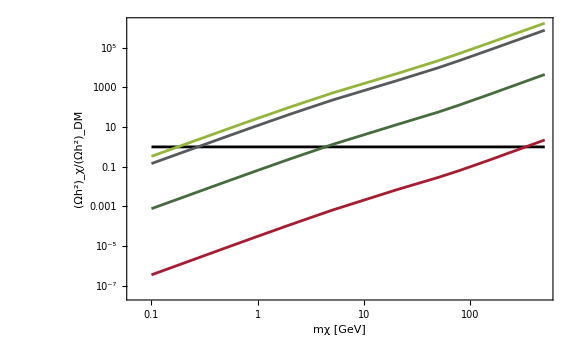

```mathematica
DMmassArray ={0.1, 0.5, 0.8,1, 2, 5,20,50, 80,150, 500};
gArray = { 0.008, 0.04, 0.01, 0.3};
RelicArray ={{}, {},{},{}};

ii = 1;
Do[
Do[

BoltzmannP = NDSolve[ {Y'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Y[x]^2 - Yeq[x]^2)/x^2, Y[1] == Yeq[1]} , Y, {x, 1, 100},MaxStepFraction->0.0001];YRescaledPrecision[x_] := Evaluate[Y[x] /. BoltzmannP[[1]]];YrescaledPrecission[x_] := YRescaledPrecision[x];RelicDensity = DensityFactor * YrescaledPrecission[100] * mass;
RelicArray[[ii]] =AppendTo[RelicArray[[ii]], RelicDensity/DensityDM],

{mass, DMmassArray} ];
ii++,
{gprime,gArray}]


RelicDensityPlot=ListLinePlot[ {Transpose[{DMmassArray,ConstantArray[1, {Length[DMmassArray]} ] }], 
Transpose[{DMmassArray, RelicArray[[1]]}],
Transpose[{DMmassArray, RelicArray[[2]]}],
Transpose[{DMmassArray, RelicArray[[3]]}],
Transpose[{DMmassArray, RelicArray[[4]]}] }, 
ScalingFunctions->{"Log", "Log"},

BaseStyle->{FontFamily->"Dosis Medium",FontSize->14},
PlotStyle->{Black,MainColor1, BackGroundColor1, Gray1, MainColor2},
Frame->True,
FrameLabel->{"mχ [GeV]", "(Ωh^2)_χ/(Ωh^2)_DM"},
FrameStyle -> Directive[{Black,Thick}],
ImageSize -> Large]
```

```mathematica
(((□_□)_□)_□)_□
```

#### Arrays for a parameter space plot

```mathematica
Clear[Y]


DMmassArray =Table[ i,{i,.1,100, .01}];
gArray =  Table[g,{g,0.001,0.3,0.001}];
RelicArray ={};
GetMass = {};
GetParams={};
SaveParams={};

Do[
Print["g_χ = ", gprime];
Do[

(*Solve Equations*) 
BoltzmannP = NDSolve[ {Y'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Y[x]^2 - Yeq[x]^2)/x^2, Y[1] == Yeq[1]} , Y, {x, 1, 100},MaxStepFraction->0.0001];YRescaledPrecision[x_] := Evaluate[Y[x] /. BoltzmannP[[1]]];YrescaledPrecission[x_] := YRescaledPrecision[x];RelicDensity = DensityFactor * YrescaledPrecission[100] * mass;
(*Print[RelicDensity];*)

(* Save Arrays *) 

If[DensityDM - 0.01≤  RelicDensity≤ DensityDM + 0.01,
GetParams=AppendTo[GetParams,{mass,gprime}];

RelicArray=AppendTo[RelicArray, RelicDensity/DensityDM],
None],

(*SaveParams=AppendTo[SaveParams,{mass,gprime, RelicDensity/DensityDM}],*)
{mass, DMmassArray} ],
{gprime,gArray}]
```

g_χ = 0.001

g_χ = 0.002

g_χ = 0.003

$Aborted

#### Parameter Space Plot

```mathematica
GetParams
SaveParams
```

{{1.1,0.02},{2.3,0.03},{2.4,0.03},{4.1,0.04},{4.2,0.04},{4.3,0.04},{4.4,0.04},{4.5,0.04},{6.6,0.05},{6.7,0.05},{6.8,0.05},{6.9,0.05},{7.,0.05},{7.1,0.05},{7.2,0.05},{9.9,0.06},{10.,0.06}}

{}

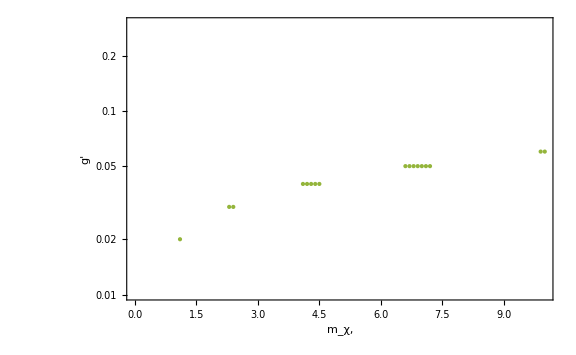

```mathematica
RelicDensityRegion= ListPlot[GetParams,


BaseStyle->{FontFamily->"Dosis Medium",FontSize->14},
PlotRange->{0.01,0.3},
ScalingFunctions->{None,"Log"},
PlotStyle->{MainColor1,PointSize[Medium]},
Frame->True,
FrameLabel->{Style["m_χ,", 18],Style["g' ", 18]}, 
FrameStyle -> Directive[{Black,Thick}],
ImageSize -> Large]
```

### Optimized Version

#### From g’ in 0.01 to 0.1

```mathematica
(*
DMmassArray=Range[0.1,100,0.01];
gArray=Range[0.001,0.3,0.001];
*)


gArray=Range[0.01,0.1,0.01];
DMmassArray=Range[.1,100,0.01];

results1=Reap[Do[Print[Subscript["g","χ"]," = ",gprime];
Do[boltzSol=NDSolve[{Y'[x]==-Mp (Pi/45)^0.5 gsToHalf[mass/x] σvtoZZApprox[gprime,mass] mass (Y[x]^2-Yeq[x]^2)/x^2,Y[1]==Yeq[1]},Y,{x,1,100},
AccuracyGoal->6,PrecisionGoal->6, MaxStepFraction->0.0001];
If[boltzSol=!={},yFinal=Y[100]/. boltzSol[[1]];
relic=DensityFactor*yFinal*mass;
If[Abs[relic-DensityDM]<=0.01,Sow[{mass,gprime,relic/DensityDM}]];];,{mass,DMmassArray}],{gprime,gArray}]][[2,1]];
```

g_χ = 0.01

g_χ = 0.02

g_χ = 0.03

g_χ = 0.04

g_χ = 0.05

g_χ = 0.06

g_χ = 0.07

g_χ = 0.08

g_χ = 0.09

g_χ = 0.1

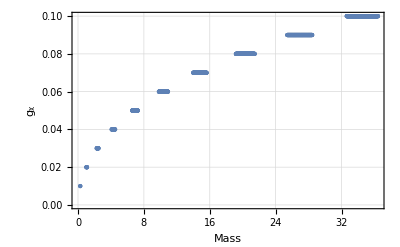

```mathematica
ListPlot[results1[[All,{1,2}]],PlotStyle->PointSize[Medium],AxesLabel->{"mass",Subscript["g","χ"]},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Mass","gᵪ"},PlotTheme->"Detailed"]
```

#### From g’ in 0.11 to 0.2

```mathematica
gArray=Range[0.11,0.2,0.01];
DMmassArray=Range[10,150,0.1];

results2=Reap[Do[Print[Subscript["g","χ"]," = ",gprime];
Do[boltzSol=NDSolve[{Y'[x]==-Mp (Pi/45)^0.5 gsToHalf[mass/x] σvtoZZApprox[gprime,mass] mass (Y[x]^2-Yeq[x]^2)/x^2,Y[1]==Yeq[1]},Y,{x,1,100},MaxStepFraction->0.0001];
If[boltzSol=!={},yFinal=Y[100]/. boltzSol[[1]];
relic=DensityFactor*yFinal*mass;
If[Abs[relic-DensityDM]<=0.01,Sow[{mass,gprime,relic/DensityDM}]];];,{mass,DMmassArray}],{gprime,gArray}]][[2,1]];
```

g_χ = 0.11

g_χ = 0.12

g_χ = 0.13

g_χ = 0.14

g_χ = 0.15

g_χ = 0.16

g_χ = 0.17

g_χ = 0.18

g_χ = 0.19

g_χ = 0.2

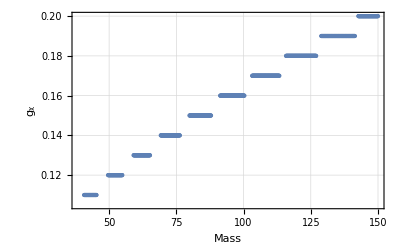

```mathematica
ListPlot[results2[[All,{1,2}]],PlotStyle->PointSize[Medium],AxesLabel->{"mass",Subscript["g","χ"]},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Mass","gᵪ"},PlotTheme->"Detailed"]
```

#### From g’ in 0.21 to 0.3

```mathematica
gArray=Range[0.21,0.3,0.01];
DMmassArray=Range[100,350,1];

results3=Reap[Do[Print[Subscript["g","χ"]," = ",gprime];
Do[boltzSol=NDSolve[{Y'[x]==-Mp (Pi/45)^0.5 gsToHalf[mass/x] σvtoZZApprox[gprime,mass] mass (Y[x]^2-Yeq[x]^2)/x^2,Y[1]==Yeq[1]},Y,{x,1,100},MaxStepFraction->0.0001];
If[boltzSol=!={},yFinal=Y[100]/. boltzSol[[1]];
relic=DensityFactor*yFinal*mass;
If[Abs[relic-DensityDM]<=0.01,Sow[{mass,gprime,relic/DensityDM}]];];,{mass,DMmassArray}],{gprime,gArray}]][[2,1]];
```

g_χ = 0.21

g_χ = 0.22

g_χ = 0.23

g_χ = 0.24

g_χ = 0.25

g_χ = 0.26

g_χ = 0.27

g_χ = 0.28

g_χ = 0.29

g_χ = 0.3

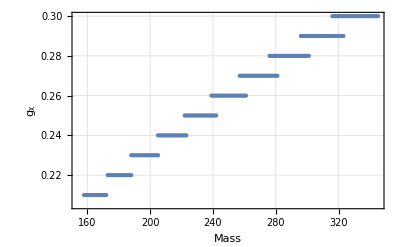

```mathematica
ListPlot[results3[[All,{1,2}]],PlotStyle->PointSize[Medium],AxesLabel->{"mass",Subscript["g","χ"]},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Mass","gᵪ"},PlotTheme->"Detailed"]
```

#### From g' in 0.002 to 0.01

```mathematica
gArray=Range[0.001,0.01,0.001];
DMmassArray=Range[0.01,10,0.005];

results4=Reap[Do[Print[Subscript["g","χ"]," = ",gprime];
Do[boltzSol=NDSolve[{Y'[x]==-Mp (Pi/45)^0.5 gsToHalf[mass/x] σvtoZZApprox[gprime,mass] mass (Y[x]^2-Yeq[x]^2)/x^2,Y[1]==Yeq[1]},Y,{x,1,100},AccuracyGoal->6,PrecisionGoal->6,MaxStepFraction->0.0001];
If[boltzSol=!={},yFinal=Y[100]/. boltzSol[[1]];
relic=DensityFactor*yFinal*mass;
If[Abs[relic-DensityDM]<=0.01,Sow[{mass,gprime,relic/DensityDM}]];];,{mass,DMmassArray}],{gprime,gArray}]][[2,1]];
```

g_χ = 0.001

g_χ = 0.002

g_χ = 0.003

g_χ = 0.004

g_χ = 0.005

g_χ = 0.006

g_χ = 0.007

g_χ = 0.008

g_χ = 0.009

g_χ = 0.01

g_χ = 0.011

g_χ = 0.012

g_χ = 0.013

g_χ = 0.014

g_χ = 0.015

g_χ = 0.016

g_χ = 0.017

g_χ = 0.018

g_χ = 0.019

g_χ = 0.02

g_χ = 0.021

g_χ = 0.022

g_χ = 0.023

g_χ = 0.024

g_χ = 0.025

g_χ = 0.026

g_χ = 0.027

g_χ = 0.028

g_χ = 0.029

g_χ = 0.03

g_χ = 0.031

g_χ = 0.032

g_χ = 0.033

g_χ = 0.034

g_χ = 0.035

g_χ = 0.036

g_χ = 0.037

g_χ = 0.038

g_χ = 0.039

g_χ = 0.04

g_χ = 0.041

g_χ = 0.042

g_χ = 0.043

g_χ = 0.044

g_χ = 0.045

g_χ = 0.046

g_χ = 0.047

g_χ = 0.048

g_χ = 0.049

g_χ = 0.05

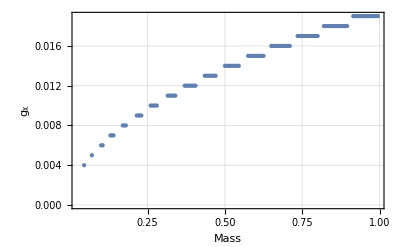

```mathematica
ListPlot[results4[[All,{1,2}]],PlotStyle->PointSize[Medium],AxesLabel->{"mass",Subscript["g","χ"]},PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Mass","gᵪ"},PlotTheme->"Detailed"]
```

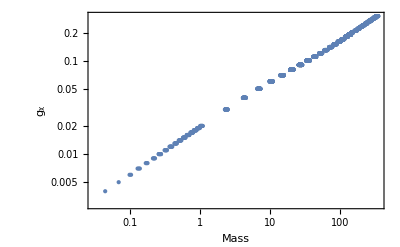

D:\Nicolás\Documents\Research\Pre-Prints\Leptophilic-Atlas\Leptophilic-Atlas-Repo\Leptophilic-Atlas-Repo\Data-Sets\RelicDensityResults.csv

```mathematica
combinedResults=Join[results4, results1,results2,results3 ];
ListPlot[combinedResults[[All,{1,2}]],PlotStyle->PointSize[Medium],AxesLabel->{"mass",Subscript["g","χ"]}, ScalingFunctions->{"Log", "Log"}, PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Mass","gᵪ"},PlotTheme->"Detailed"]
Export["D:\\Nicolás\\Documents\\Research\\Pre-Prints\\Leptophilic-Atlas\\Leptophilic-Atlas-Repo\\Leptophilic-Atlas-Repo\\Data-Sets\\RelicDensityResults.csv",combinedResults]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["RelicDensityResults.csv"]]]
```

```mathematica
(-I)^5
```

-ⅈ

## Assymetric Dark Matter

Yield:

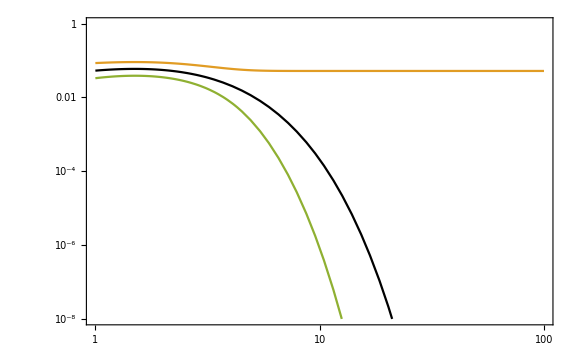

```mathematica
mass = 5;
gprime=0.03;

BoltzmannEqs = NDSolve[ {
Yp'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, Ym'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, 
Yp[1] == 0.99 Yeq[1], 
Ym[1] == Yeq[1] - Yp[1]} , 
{Yp, Ym}, {x, 1, 100},MaxStepFraction->0.0001];
Y[x_] := Evaluate[{Yp[x], Ym[x]}/. BoltzmannEqs[[1]]];
Ychi[x_]:= Y[x][[1]] ;
YchiBar[x_]:= Y[x][[2]] ;

LogLogPlot[{Yeq[x], Ychi[x], YchiBar[x]}, {x,1,100}, PlotRange->{1*^-8, 1}, 
Frame->True,
PlotStyle->{Black, MainColor1, MainColor2}, 
FrameStyle -> Directive[{Black,Thick}],
ImageSize->Large]
```

Relic density:

NDSolve::ndsz: At x == 1., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At x == 1., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

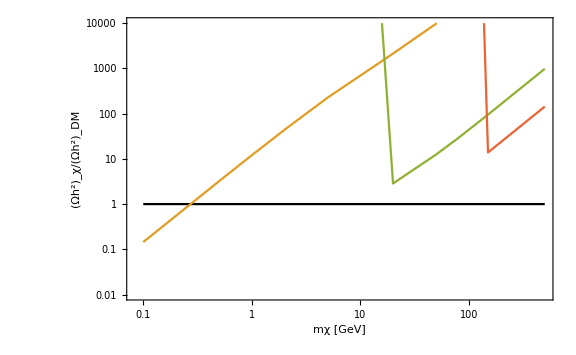

```mathematica
DMmassArray ={0.1, 0.5, 0.8,1, 2, 5,20,50, 80,150, 500};
gArray = {  0.01, 0.06, 0.1, 0.2};
RelicArrayChi ={{}, {},{},{}};
RelicArrayChiBar={{}, {},{},{}};

ii = 1;
Do[
Do[

BoltzmannEqs= NDSolve[ {
Yp'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, Ym'[x] == - Mp (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, 
Yp[1] == 0.5Yeq[1], 
Ym[1] == Yeq[1] - Yp[1]} , 
{Yp, Ym}, {x, 1, 100},MaxStepFraction->0.0001];
Y[x_] := Evaluate[{Yp[x], Ym[x]}/. BoltzmannEqs[[1]]];
Ychi[x_]:= Y[x][[1]] ;
YchiBar[x_]:= Y[x][[2]] ;

Ochi = DensityFactor *  Ychi[100] * mass;
OchiBar = DensityFactor *  YchiBar[100] * mass;
RelicArrayChi[[ii]] =AppendTo[RelicArrayChi[[ii]], Ochi/DensityDM];
RelicArrayChiBar[[ii]] =AppendTo[RelicArrayChiBar[[ii]], OchiBar/DensityDM],
{mass, DMmassArray} ];
ii++,
{gprime,gArray}]

RelicDensityPlot=ListLinePlot[ {Transpose[{DMmassArray,ConstantArray[1, {Length[DMmassArray]} ] }], 
Transpose[{DMmassArray, RelicArrayChi[[1]]}],
Transpose[{DMmassArray, RelicArrayChi[[2]]}],
Transpose[{DMmassArray, RelicArrayChi[[3]]}],
Transpose[{DMmassArray, RelicArrayChi[[4]]}] }, 
ScalingFunctions->{"Log", "Log"},
PlotRange->{0.01, 1*^4},

BaseStyle->{FontFamily->"Dosis Medium",FontSize->14},
PlotStyle->{Black,MainColor1, BackGroundColor1, Gray1, MainColor2},
Frame->True,
FrameLabel->{"mχ [GeV]", "(Ωh^2)_χ/(Ωh^2)_DM"},
FrameStyle -> Directive[{Black,Thick}],
ImageSize -> Large]
```

```mathematica
mass = 50;
gprime = 0.1;

BoltzmannEqs= NDSolve[ {
Yp'[x] == -  (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, Ym'[x] == -  (Pi /45)^0.5 gs to half[mass/x] σvtoZZApprox[gprime, mass]  mass (Yp[x] Ym[x] - Yeq[x]^2)/x^2, 
Yp[1] == 0.5Yeq[1], 
Ym[1] == Yeq[1] - Yp[1]} , 
{Yp, Ym}, {x, 1, 100},MaxStepFraction->0.0001];
Y[x_] := Evaluate[{Yp[x], Ym[x]}/. BoltzmannEqs[[1]]];
Ychi[x_]:= Y[x][[1]] ;
YchiBar[x_]:= Y[x][[2]] ;

Ochi = DensityFactor *  Ychi[100] * mass;
OchiBar = DensityFactor *  YchiBar[100] * mass;
Ochi/DensityDM
```

1.77178×10^9

```mathematica
Integrate[ 2,{x,0,2}]
```

4